# Film Calculations

```mathematica
T[ k_, d_]:=({{Cos[k d], ⅈ ω/(c k)Sin[k d]}, {ⅈ (c k)/ω Sin[k d], Cos[k d]}});
```

### Two-layer silicon/silica stack

```mathematica
Tcrys=T[k2,d2].T[k1, d1]/.{k1->3.45 ω/c,k2->1.44 ω/c};
```

```mathematica
result=Inverse[({{1, 1}, {-1, 1}})].Inverse[Tcrys].({{1, 1}, {-1, 1}}).{t,0};
```

```mathematica
t″=t/result[[1]];
```

```mathematica
r″=result[[2]]/.t->t″;
```

```mathematica
cval=3*10^8*10^6;
ωval=2π cval / 1.55;
```

```mathematica
Plot3D[Evaluate[Abs[t″]/.c->cval/.ω-> ωval/.d1-> 1/f1/.d2->1/f2],{f1,1,8},{f2,1,8},AxesLabel->{"Silicon: 1/d_1 (μm^-1)","Silica: 1/d_2 (μm^-1)",None},PlotLegends->{"Cell["|t|",ExpressionUUID->"81a58755-2e8e-400f-9e0f-63ac1e74c18a"]"},ImageSize->Large]
```

-Graphics3D-

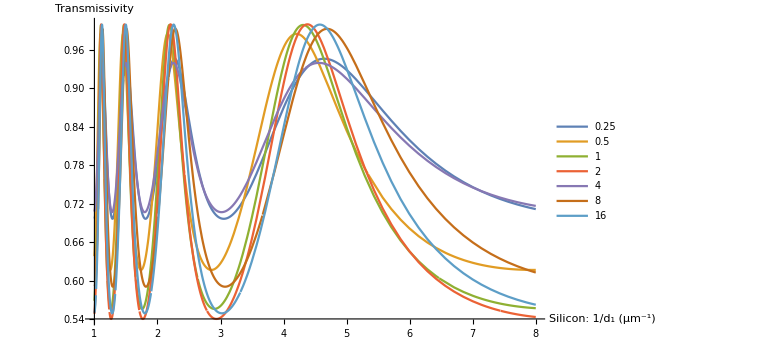

```mathematica
Plot[Evaluate[Abs[t″]/.c->cval/.ω-> ωval/.d1-> 1/f1/.d2->1/f2/.f2->{.25,.5,1,2,4,8,16}],{f1,1,8},AxesLabel->{"Silicon: 1/d_1 (μm^-1)","Transmissivity"},PlotLegends->{.25,.5,1,2,4,8,16},ImageSize->Large]
```

### Compare with:

```mathematica
-Graphics-;
```